## Coverage over a nomal distribution Mary Burbage and Aaron Becker Lesson: use RevolutionPlot3D, not Plot3D, http://mathworld.wolfram.com/BivariateNormalDistribution.html

### Distribution after a random walk of length r~U[0,1] at angle θ~U[0,2π]. We are sure about this result

```mathematica
Limit[ (dr/rmax dθ/(2π))/(dθ/2(2 r dr +dr^2)),{dr->0}]  (*alternate way to prove this.  Only defined inside circle with radius rmax*)
```

```mathematica
rmax = 0.4
```

```mathematica
{1/(2 π r rmax)}
h = Convolve[If[r<rmax,1/(2 π r rmax) ,0],UnitBox[r],r,y]
```

{0.397887/r}

Piecewise[{{0., y≥0.9}, {(0.-1.25 ⅈ)+0.795775 ArcTanh[2. y], y<-0.1}, {-0.397887 Log[-1.25+2.5 y], True}}]

```mathematica
{(-Log[-1+2 y]+Log[1+2 y])/(2 π rmax)}
```

```mathematica
{(-Log[-1+2 y]+Log[1+2 y])/(2 π rmax)}
```

{0.397887 (-Log[-1+2 y]+Log[1+2 y])}

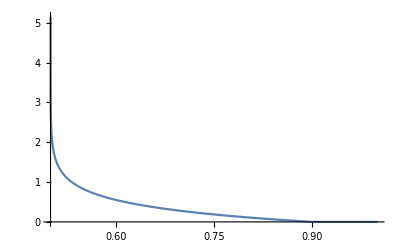

```mathematica
Plot[h,{y,0,1},PlotRange->All]
```

```mathematica
D[{√(x^2+y^2),ArcTan[y,x]},{{x,y}}]//MatrixForm
```

(x/(√(x^2+y^2)) | y/(√(x^2+y^2))
y/(x^2+y^2) | -x/(x^2+y^2))

```mathematica
FullSimplify[Det[D[{√(x^2+y^2),ArcTan[x,y]},{{x,y}}]]]
```

1/(√(x^2+y^2))

```mathematica
-1/(√(x^2+y^2))*1/(2π)
```

-1/(2 π √(x^2+y^2))

```mathematica
Convolve[E^((-x^2-y^2)/(1/10)),UnitBox[x/2,y/2],{x,y},{r,s}]
```

1/40 π (Erf[√10 (-1+r)]-Erf[√10 (1+r)]) (Erf[√10 (-1+s)]-Erf[√10 (1+s)])

```mathematica
Plot3D[E^((-x^2-y^2)/(1/4)),{x,-3,3},{y,-3,3},PlotRange->All]
Plot3D[UnitBox[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[1/40 π (Erf[√10 (-1+r)]-Erf[√10 (1+r)]) (Erf[√10 (-1+s)]-Erf[√10 (1+s)]),{r,-3,3},{s,-3,3},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[If[√(x^2+y^2)<rmax,1/(2 π rmax √(x^2+y^2)) ,0],{x,-rmax,rmax},{y,-rmax,rmax},MaxRecursion->5,AxesLabel->{"X Position (m)","Y Position (m)",Probability},ImageSize->Large]
```

-Graphics3D-

```mathematica
Convolve[If[√(x^2+y^2)<1,1/(2 π √(x^2+y^2)) ,0],UnitBox[x,y],{x,y},{r,s}]
```

```mathematica
(*simpler function that also takes maybe forever to compute*)
Convolve[If[√(x^2+y^2)<1,1/π ,0],UnitBox[x,y],{x,y},{r,s}]
```

$Aborted

```mathematica
Plot3D[1/(2 π √(x^2+y^2)),{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<1],PlotRange->{Automatic,Automatic,{0,1}}]
```

-Graphics3D-

```mathematica
TransformedDistribution[{r Cos[θ],r Sin[θ]},{r\[Distributed]UniformDistribution[{0,1}],θ\[Distributed]UniformDistribution[{0,2π}]}]
```

TransformedDistribution[{x1 Cos[x2],x1 Sin[x2]},{x1\[Distributed]UniformDistribution[{0,1}],x2\[Distributed]UniformDistribution[{0,2 π}]}]

```mathematica
d10e5=RandomVariate[TransformedDistribution[{r Cos[θ],r Sin[θ]},{r\[Distributed]UniformDistribution[{0,1}],θ\[Distributed]UniformDistribution[{0,2π}]}],1000000];
Histogram3D[d10e5,PerformanceGoal->"Speed"]
```

-Graphics3D-

```mathematica
Histogram3D[d10e5,50,PerformanceGoal->"Speed"]
```

-Graphics3D-

```mathematica
Histogram3D[RandomVariate[TransformedDistribution[{r Cos[θ],r Sin[θ]},{r\[Distributed]UniformDistribution[{0,1}],θ\[Distributed]UniformDistribution[{0,2π}]}],10000]]
```

-Graphics3D-

```mathematica
Clear[x,y];PDF[TransformedDistribution[{r Cos[θ],r Sin[θ]},{r\[Distributed]UniformDistribution[{0,1}],θ\[Distributed]UniformDistribution[{0,2π}]}],{x,y}]
```

PDF[TransformedDistribution[{x1 Cos[x2],x1 Sin[x2]},{x1\[Distributed]UniformDistribution[{0,1}],x2\[Distributed]UniformDistribution[{0,2 π}]}],{x,y}]

```mathematica
Plot3D[PDF[TransformedDistribution[{x1 Cos[x2],x1 Sin[x2]},{x1\[Distributed]UniformDistribution[{0,1}],x2\[Distributed]UniformDistribution[{0,2 π}]}],{x,y}],{x,-3,3},{y,-3,3}]
```

$Aborted

### Plot3D

```mathematica
Normal2[x_,y_,σ_]:=1/(2π σ)ⅇ^(-1/(2 σ^2)(x^2+y^2))
Normal2onepass[x_,y_,σ_,r_]:=1/(2π σ)ⅇ^(-1/(2 σ^2)(x^2+y^2))If[x^2+y^2<r^2,.1,1]
```

```mathematica
Plot3D[Normal2[x,y,2],{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Normal2onepass[x,y,2,3],{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

### RevolutionPlot3D

```mathematica
Normal2rev[x_,σ_]:=1/(2π σ)ⅇ^(-1/(2 σ^2)(x^2))
Normal2revonepass[x_,σ_,r_]:=1/(2π σ)ⅇ^(-1/(2 σ^2)(x^2))If[x<r,.5,1]
```

```mathematica
RevolutionPlot3D[Normal2rev[x,2],{x,0,8},PlotRange->{{-5,5},{-5,5},All}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Normal2revonepass[x,2,3],{x,0,8},PlotRange->{{-5,5},{-5,5},All},PlotLabel->{"50% probability removed for r<2"}]
```

-Graphics3D-

### Let's assume the drone covers an area of size a every second, and that this area is cleared in concentric circles (a gross simplification).

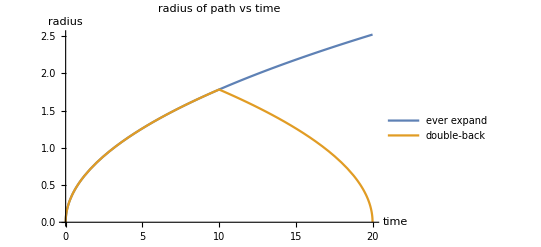

```mathematica
Plot[Evaluate[{√(a*t/π),If[t<10,√(a*t/π),(√(a (20-t)))/(√π)]}/.{a->1}],{t,0,20},PlotLabel-> "radius of path vs time",AxesLabel->{"time","radius"},PlotLegends->{"ever expand","double-back"}]
```

### What is r[t], the radius of the area cleared by a drone as a function of time? AreaCleared = a*t. AreaCleared = π r^2 Current Radius r[t] = √((a*t)/π) Current Radius path 2 r2[t] = √((10a-a*(t-10))/π)=(√(a (20-t)))/(√π)

```mathematica
-(-1+ⅇ^(-(√((a*t)/π))^2/(2 σ^2))) KillFrac
```

(1-ⅇ^(-(a t)/(2 π σ^2))) KillFrac

```mathematica
(*Normal probability within radius of r*)
Clear[σ]
2π∫_0^r x(1/(2π σ^2)ⅇ^(-1/(2 σ^2)(x^2)))ⅆx
```

1-ⅇ^(-r^2/(2 σ^2))

```mathematica
(*Normal probability collected when spiralling out *)
Clear[T,a,σ,KillFrac,rt1,rt2]
KillFrac 2π∫_0^rt1[t] x(1/(2π σ^2)ⅇ^(-1/(2 σ^2)(x^2)))ⅆx
```

-(-1+ⅇ^(-rt1[t]^2/(2 σ^2))) KillFrac

```mathematica
(*Normal probability collected when spiralling back in when t = T *)
Clear[T,a,σ,KillFrac,rt1,rt2]
FullSimplify[KillFrac 2π∫_0^rt1[T] x(1/(2π σ^2)ⅇ^(-1/(2 σ^2)(x^2)))ⅆx+KillFrac(1-KillFrac)2π∫_rt2[t,T]^rt1[T] x (1/(2π σ^2)ⅇ^(-1/(2 σ^2)(x^2)))ⅆx]
```

(1+ⅇ^(-rt1[T]^2/(2 σ^2)) (-2+KillFrac)-ⅇ^(-rt2[t,T]^2/(2 σ^2)) (-1+KillFrac)) KillFrac

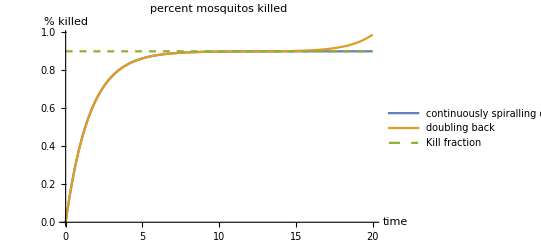

```mathematica
rt1[t_] := √(t/π);
rt2[t_,T_] := (√(2T-t))/(√π);
T = 10;
KillFrac = .9;
σ = 1/2;

Plot[{-(-1+ⅇ^(-rt1[t]^2/(2 σ^2))) KillFrac,If[t<T,-(-1+ⅇ^(-rt1[t]^2/(2 σ^2))) KillFrac,(1+ⅇ^(-rt1[T]^2/(2 σ^2)) (-2+KillFrac)-ⅇ^(-rt2[t,T]^2/(2 σ^2)) (-1+KillFrac)) KillFrac],KillFrac},{t,0,2T},PlotStyle->{Automatic,Automatic,Dashed},PlotLabel-> "percent mosquitos killed",AxesLabel->{"time","% killed"},PlotLegends->{"continuously spiralling out","doubling back","Kill fraction"},PlotRange->All]
```

```mathematica
Manipulate[Module[{rt1,rt2},rt1[t_] := √(t/π);
rt2[t_,T_] := (√(2T-t))/(√π);
Plot[{-(-1+ⅇ^(-rt1[t]^2/(2 σ^2))) KillFrac,If[t<T,-(-1+ⅇ^(-rt1[t]^2/(2 σ^2))) KillFrac,(1+ⅇ^(-rt1[T]^2/(2 σ^2)) (-2+KillFrac)-ⅇ^(-rt2[t,T]^2/(2 σ^2)) (-1+KillFrac)) KillFrac]},{t,0,2T},PlotLabel-> "percent mosquitos killed",AxesLabel->{"time","% killed"},

Epilog->{Line[{{T,0},{T,1}}]},PlotLegends->{"continuously spiralling out","doubling back"},PlotRange->All]],
{{T, 10},1/100,100},
{{KillFrac,.5},1/100,1} ,
{{σ , 2/3},1/100,10}]
```

## ITEM: Simulate mosquitoes always reforming normal dist. This is a discrete simulation where you kill 90% of the mosquitoes that are at the robot’s current radius every 1 second. Staying at the center maximizes kill rate -- what is the kill rate as a function of time? # of surviving mosquitoes => n(t) = n(0)*(1-k*p)^t # of dead mosquitoes => d(t) = n(0)-n(t) = n(0)*(1-(1-k*p)^t) k = kill percentage, p = percentage of mosquitoes in kill zone

## TODO: Generate Markov transition matrix P for a square area A with a sticky wall effect -- make the transition out of the wall cells to be f of normal. Tests: run boustropheon, compare to running along the wall as a function of f and area A.

## TODO: generate a 3x3 markov transition matrix P that has a normal stationary distribution w. We want P to be symmetric.

### try in 1 D. This worked great for the 3x3 matrix and failed for 5x5

```mathematica
P=({{1-b, b, 0}, {a, 1-2a, a}, {0, b, 1-b}});
```

```mathematica
Assuming[a>0&&a<1/2 && b>0&&b<1,Limit[MatrixPower[P,n],n->∞]]//MatrixForm
```

(a/(2 a+b) | b/(2 a+b) | a/(2 a+b)
a/(2 a+b) | b/(2 a+b) | a/(2 a+b)
a/(2 a+b) | b/(2 a+b) | a/(2 a+b))

```mathematica
P5a=({{1-a, a, 0, 0, 0}, {2 a, 1-5a, 3a, 0, 0}, {0, 4 a, 1-8a, 4a, 0}, {0, 0, 3a, 1-5a, 2a}, {0, 0, 0, a, 1-a}});
```

```mathematica
MatrixForm[{{1-a,a,0,0,0},{2 a,1-5 a,3 a,0,0},{0,4 a,1-8 a,4 a,0},{0,0,3 a,1-5 a,2 a},{0,0,0,a,1-a}}]
```

```mathematica
Assuming[a>0&&a<1/8 
,Limit[MatrixPower[P5a,n],n->∞]]//MatrixForm
```

(8/27 | 4/27 | 1/9 | 4/27 | 8/27
8/27 | 4/27 | 1/9 | 4/27 | 8/27
8/27 | 4/27 | 1/9 | 4/27 | 8/27
8/27 | 4/27 | 1/9 | 4/27 | 8/27
8/27 | 4/27 | 1/9 | 4/27 | 8/27)

```mathematica
P5=({{1-d, d, 0, 0, 0}, {b, 1-b-c, c, 0, 0}, {0, a, 1-2a, a, 0}, {0, 0, c, 1-b-c, b}, {0, 0, 0, d, 1-d}});
```

```mathematica
MatrixPower[P5,n]//Simplify
```

{{(2^(-2-n) (52+c d √1 √1 (1)^n))/((c d+2 a (b+d)) √(b^2+(c-d)^2+2 b (c+d)) √(4 a^2+b^2+(c-d)^2-4 a (b-c+d)+2 b (c+d))),-1/1,1/1,-1/1,(2^(-2-n) (1))/((c d+2 a (b+d)) √1 √(4 a^2+b^2+1^2-1+2 b (c+d)))},3,{1}}
 |  |  |  |

```mathematica
Assuming[a>0&&a<1/2 
&& b>0&&b<1/2
&&c>0&&c<1/2
&&d>0&&d<1/2,Limit[MatrixPower[P5,n],n->∞]]//MatrixForm
```

Limit[MatrixPower[P5,n],n→∞]

## TODO: generate a 5x5 markov transition matrix P that has a normal stationary distribution w. We want P to be symmetric.